# One-loop fermion mass shift in Yukawa theory (Fig 19) (takes 5~10 minutes)

#### Analytic large truncation result

```mathematica
AnalyticFermionMassShift[mϕ_,Δmax_]:=((√(-mϕ^2+4))/mϕ ArcSec[2/mϕ]+Log[Δmax])/(2 π);
```

#### Mass Matrices

Mass matrix for [ϕψ] states from boson mass ϕ^2 and from fermion mass ψ 1/∂ψ

```mathematica
BosonϕψMassMatrix[n_,m_]=2 √(((l+1)(l+3))/((lp+1)(lp+3))(l+2)(lp+2))/.{l->Min[n,m],lp->Max[n,m]};
FermionϕψMassMatrix[n_,m_]=(-1)^(l+lp)((l+2)/(lp+2))√(((l+1)(l+3))/((lp+1)(lp+3))(l+2)(lp+2))/.{l->Min[n,m],lp->Max[n,m]};
```

Mass matrix for [ψψ] states from fermion mass ψ 1/∂ψ

```mathematica
Fermion2ψMassMatrix[l_,lp_]:=√(((1+lm) (2+lm) (3+lm) (4+lm) (5+2 lm) (5+2 lM))/((1+lM) (2+lM) (3+lM) (4+lM)))/.{lm->Min[l,lp],lM->Max[l,lp]};
```

#### Cubic Yukawa term matrix elements ⟨ψ|ϕψ 1/∂ψ|[ϕψ]_l⟩ between |ψ⟩ state and |[ϕψ]_l⟩ states

```mathematica
CubicYukawaMatrixElement[m_]:=(-1)^m(m+If[EvenQ[m],3,1])^2 √(2/((m+1)(m+2)(m+3)));
```

#### Compute mass shift using second order time-independent perturbation theory

Expand to second order in the Yukawa term, but work exactly in mass term: 
H = H_mass+V_Yukawa, Δm_ψ^2= ∑_k ⟨ψ|ϕψ1/∂ψ|[ϕψ]_k⟩/(m_ψ^2-μ_k^2), where |[ϕψ]_k⟩ are eigenstates of H_mass.
Use units with m_ψ=1

```mathematica
Monitor[For[LMaxJacobi=25,LMaxJacobi≤200,LMaxJacobi*=2,
For[ms=1/4,ms≤2,ms*=2^(1/20),
(* Make the mass matrix for [ϕψ] states *)
MϕψJacobi=Outer[ms^2 BosonϕψMassMatrix[#1,#2]+FermionϕψMassMatrix[#1,#2]&,Range[0,LMaxJacobi],Range[0,LMaxJacobi]]//N;
(* Get eigenvectors and eigenvalues of mass term *)
JacobiϕψMassEvecs=Eigenvectors[MϕψJacobi]//Reverse//Transpose;
JacobiϕψMassEvals=Eigenvalues[MϕψJacobi]//Reverse;
(* Compute overlap of |ψ⟩ state with mass term eigenstates *)
JacobiϕψOverlap=CubicYukawaMatrixElement/@Range[0,LMaxJacobi];
JacobiϕψOverlapMassBasis=JacobiϕψOverlap.JacobiϕψMassEvecs;
(* Compute second order time independent perturbation theory energy shift *)
mfvals[LMaxJacobi,ms]=1/(16π)Sum[JacobiϕψOverlapMassBasis[[i]]^2/(JacobiϕψMassEvals[[i]]-1),{i,Length[JacobiϕψMassEvals]}];
];
];,
{LMaxJacobi,ms}]
```

```mathematica
mymsvals=2^(-2+#/20)&/@Range[0,60];
```

#### Plot the numeric mass shifts

Compare numeric mass shifts with analytic results, for Δmax=25,50,100,200.  γ was chosen by hand

First, compare as a function of m_ϕ/m_ψ

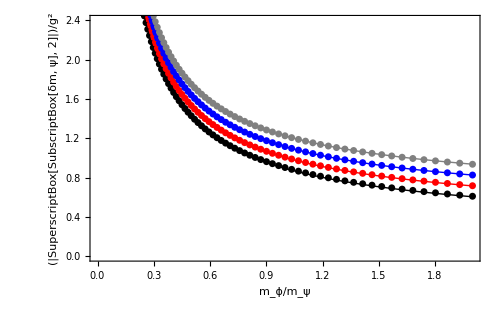

```mathematica
γγ=1.8;
Show[ListPlot[{{#,4mfvals[25,#]}&/@mymsvals,{#,4mfvals[50,#]}&/@mymsvals,{#,4mfvals[100,#]}&/@mymsvals,{#,4mfvals[200,#]}&/@mymsvals},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->22},ImageSize->500,FrameLabel->{"m_ϕ/m_ψ","(|SuperscriptBox[SubscriptBox[δm, ψ], 2]|)/g^2"},RotateLabel->False,PlotRange->{0,2.4},PlotStyle->{{Black,PointSize[0.010]},{Red,PointSize[0.010]},{Blue,PointSize[0.010]},{Gray,PointSize[0.010]}}],Plot[{AnalyticFermionMassShift[mϕ,25]+Log[γγ]/(2π),AnalyticFermionMassShift[mϕ,50]+Log[γγ]/(2π),AnalyticFermionMassShift[mϕ,100]+Log[γγ]/(2π),AnalyticFermionMassShift[mϕ,200]+Log[γγ]/(2π)},{mϕ,1/4,2},PlotRange->All,PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick},{Gray,Thick}}]]
```

Then, compare as a function of Δ_max (shift L_max by 0.5 because Δ_ψ=1/2)

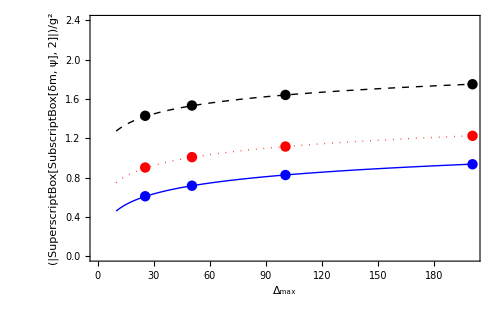

```mathematica
Show[ListPlot[{{#+0.5,4mfvals[#,1/2]}&/@{25,50,100,200},{#+0.5,4mfvals[#,1]}&/@{25,50,100,200},{#+0.5,4mfvals[#,2]}&/@{25,50,100,200}},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->22},ImageSize->500,FrameLabel->{"Δ_max","(|SuperscriptBox[SubscriptBox[δm, ψ], 2]|)/g^2"},RotateLabel->False,PlotRange->{0,2.4},PlotStyle->{{Black,PointSize[0.015]},{Red,PointSize[0.015]},{Blue,PointSize[0.015]},{Gray,PointSize[0.010]}}],Plot[{AnalyticFermionMassShift[1/2,Δ]+Log[γγ]/(2π),AnalyticFermionMassShift[1,Δ]+Log[γγ]/(2π),AnalyticFermionMassShift[2,Δ]+Log[γγ]/(2π)},{Δ,10,200},PlotStyle->{{Black,Thick,Dashed},{Red,Thick,Dotted},{Blue,Thick}}]]
```